```mathematica
n=10;
lis = Range[n*n];
lis=Partition[lis,10]
RightHopping = Map[RotateLeft,lis](*Right Hopping*)
LeftHopping = Map[RotateRight,lis](*Left Hopping*)
UpDirection=lis+n;
DownDirection=lis-n;
f1[x_List]:=Select[x,#>100&];(*筛选向上hopping的最后一行的周期位置*)
f2[x_List]:=Select[x,#<=0&];(*筛选向下Hopping的第一行的周期位置*)
U1=Flatten[Map[f1,UpDirection]]-n*n;(*最后一行向上Hopping的索引修正*)
D1 =Flatten[Map[f2,DownDirection]]+n*n;(*第一行向下Hopping的索引修正*)
UpDirection = Append[UpDirection =Delete[UpDirection,-1],U1]
DownDirection = Prepend[DownDirection =Delete[DownDirection,1],D1]
```

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100}}

{{2,3,4,5,6,7,8,9,10,1},{12,13,14,15,16,17,18,19,20,11},{22,23,24,25,26,27,28,29,30,21},{32,33,34,35,36,37,38,39,40,31},{42,43,44,45,46,47,48,49,50,41},{52,53,54,55,56,57,58,59,60,51},{62,63,64,65,66,67,68,69,70,61},{72,73,74,75,76,77,78,79,80,71},{82,83,84,85,86,87,88,89,90,81},{92,93,94,95,96,97,98,99,100,91}}

{{10,1,2,3,4,5,6,7,8,9},{20,11,12,13,14,15,16,17,18,19},{30,21,22,23,24,25,26,27,28,29},{40,31,32,33,34,35,36,37,38,39},{50,41,42,43,44,45,46,47,48,49},{60,51,52,53,54,55,56,57,58,59},{70,61,62,63,64,65,66,67,68,69},{80,71,72,73,74,75,76,77,78,79},{90,81,82,83,84,85,86,87,88,89},{100,91,92,93,94,95,96,97,98,99}}

{{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,8,9,10}}

{{91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90}}

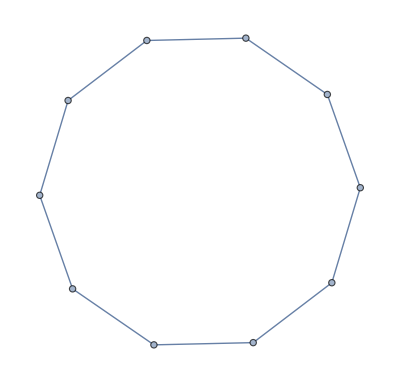
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
t1 =MapThread[UndirectedEdge,{lis,RightHopping},2];
Map[Graph[#,GraphLayout->"SpringEmbedding"]&,t1]
```

```mathematica
DirectedEdge
```

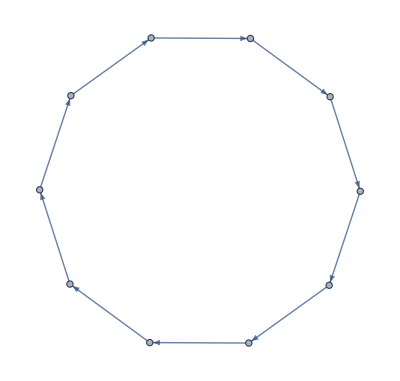

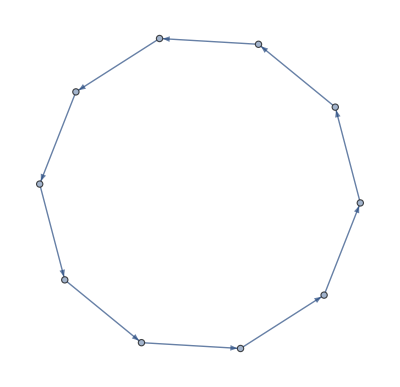

```mathematica
t1 =MapThread[DirectedEdge,{lis,RightHopping},2];
t1c =MapThread[DirectedEdge,{RightHopping,lis},2];
Map[Graph[#,GraphLayout->"SpringEmbedding"]&,t1][[1]]
Map[Graph[#,GraphLayout->"SpringEmbedding"]&,t1c][[1]]
```